```mathematica
Clear[Si,s,LT,avgManualToll,avgElectronicTollRate]
Si=3;(*Input Lanes*)
s=9;(*Booths*)
LT=3;(*total # of lanes in a partition*)
(*Solve[s==(Si)*(LT),(*input variable to solve for*)]*)
avgManualToll=1/(350/60^2)(*rate of human collected tolls*);
avgElectronicTollRate=1/(1200/60^2)(*rate of electronically collected tolls*);
(*Functions to compute μ*)
Clear[ETCRate]
ETCRate[ETC_]:=1/avgElectronicTollRate
Clear[HRate]
HRate[H_]:=1/avgManualToll
```

```mathematica
λ=ErlangDistribution[5.6/30,10/30];
```

```mathematica
Clear[ModelFunctionElectronic]
(*Returns mean system time for electronic systems*)
ModelFunctionElectronic[λ_,ETC_,H_]:=
QueueProperties[
QueueingProcess[
λ/(ETC+H),
ETCRate[ETC],
ETC
],
"MeanSystemTime"
]
```

```mathematica
Clear[ModelFunctionElectronicQueueTable]
(*Returns mean system time for manual systems*)
ModelFunctionElectronicQueueTable[λ_,ETC_,H_]:=
QueueProperties[
QueueingProcess[
λ/(ETC+H),
ETCRate[ETC],
ETC],"ServiceRate"]
```

```mathematica
Clear[ModelFunctionManual]
(*Finds MTC Mean System Time*)
ModelFunctionManual[λ_,ETC_,H_]:=
QueueProperties[
QueueingProcess[
λ/(ETC+H),
HRate[H],
H],
"MeanSystemTime"]
```

```mathematica
Clear[ModelFunctionManualQueueTable]
(*Finds MTC Service Rate*)
ModelFunctionManualQueueTable[λ_,ETC_,H_]:=
QueueProperties[
QueueingProcess[
λ/(ETC+H),
HRate[H],
H],
"ServiceRate"]
```

```mathematica
Clear[currentSystemFunction]
(*Finds the Mean System Time*)
currentSystemFunction[λ_,ETC_,H_]:=
{
Table[
QueueProperties[
QueueingProcess[(λ)/(ETC+H),ETCRate[ETC]
],"MeanSystemTime"],
{i,1,ETC}
],Table[
QueueProperties[
QueueingProcess[(λ)/(ETC+H),HRate[H]
],"MeanSystemTime"],{i,1,H}
]
}
```

```mathematica
Clear[avgFunction]
avgFunction[λ_,ETC_,H_]:=Total[Flatten[currentSystemFunction[ETC,H,λ]]]/(ETC+H)//N
```

Functions

```mathematica
Clear[EdgeFunction]
(*Building initial to partition edges*)
EdgeFunction[Si_,s_]:=Table[DirectedEdge["InitialVertex",Subscript[p, i]],{i,1,s/Si}]
```

```mathematica
Clear[PartitionEdgeFunction]
(*Building partition to tollbooth edges*)
PartitionEdgeFunction[Si_,s_,LT_]:=
Flatten[
Table[
Map[
DirectedEdge[Subscript[p, i],#]&,
Partition[
Map[
Subscript[B, #]&,Range[s]
],
{LT}
][[i]]
],
{i,1,Si}
]
]
```

```mathematica
Clear[MergeLaneFunction]
(*Building tollbooth to merge edges*)
MergeLaneFunction[Si_,s_,LT_]:=
Flatten[
Table[
Map[
DirectedEdge[#,Subscript[m, i]]&,
Partition[
Map[
Subscript[B, #]&,Range[s]
],
{LT}
]
[[i]]
],
{i,1,Si}
]
]
```

```mathematica
Clear[EdgeFunction2]
(*Building merge to end edges*)
EdgeFunction2[Si_,s_]:=Table[
DirectedEdge[
Subscript[m, i],"EndVertex"
],
{i,1,s/Si}
]
```

```mathematica
Clear[currentModelEdges]
currentModelEdges[servers_]:=
Flatten[
{
Table[
DirectedEdge[
"InitialVertex",Subscript[m, i]],
{i,servers}
],
Table[
DirectedEdge[
Subscript[m, i],"EndVertex"],
{i,servers}
]
}
]
```

```mathematica
Clear[currentModelGraph]
currentModelGraph[servers_,ETC_,H_,λ_]:=
Graph[
Flatten[
{
"InitialVertex",
"EndVertex",
Table[Subscript[m, i],{i,1,servers}]
}
],
currentModelEdges[servers],
ImageSize->Large,
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Bottom},
VertexStyle->
Table[
Subscript[m, i]->Red,{i,servers,servers-ETC+1,-1}],
EdgeWeight->Flatten[
{
Table[
DirectedEdge[Subscript[m, i],"EndVertex"]->
Ceiling[servers/2]-i+1,
{i,1,Floor[servers/2]}
],
Table[
DirectedEdge[Subscript[m, i],"EndVertex"]->
i-Floor[servers/2],
{i,servers,Ceiling[servers/2],-1}
],
Table[
DirectedEdge["InitialVertex",Subscript[m, i]]->
ModelFunctionElectronic[λ,ETC,H],
{i,servers,servers-ETC+1,-1}
],
Table[
DirectedEdge["InitialVertex",Subscript[m, i]]->
ModelFunctionManual[λ,ETC,H],
{i,1,servers-ETC+1}
]
}
],
VertexLabels->"Name",
EdgeLabels->"EdgeWeight",ImageSize->1000
]
```

```mathematica
Clear[GraphFunction]
(*Creates the proposed model graph*)
GraphFunction[Si_,s_,LT_,λ_,ETC_,H_]:=
Graph[
Union[
EdgeFunction[Si,s],
PartitionEdgeFunction[Si,s,LT],
MergeLaneFunction[Si,s,LT],
EdgeFunction2[Si,s]],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Bottom},
VertexStyle->
Flatten[
(*Specifies the vertices that represent ETC booths*)
{Table[
PartitionEdgeFunction[
Si,s,LT][[i,2]]->Red,
{i,s,s-Si+1,-1}
],
Table[
PartitionEdgeFunction[
Si,s,LT][[i,2]]->Red,
{i,2,Ceiling[s/2]}
]
}
],
EdgeWeight->Flatten[
{
(*Merge Lane Edge Weights, needs to be modified for different partition sets*)
Table[
Partition[
MergeLaneFunction[
Si,s,LT],
{3}
]
[[j,i]]->
i
,{i,LT,1,-1},
{j,2,3}
],
Table[
Partition[
MergeLaneFunction[
Si,s,LT],
{3}
]
[[1,i]]->
LT-i+1
,{i,1,LT}],

(*Queue Lane Edge Weights*)
Map[#->ModelFunctionManual[λ,ETC,H]&,
Complement[
PartitionEdgeFunction[Si,s,LT],
Flatten[
{Table[
PartitionEdgeFunction[Si,s,LT][[i]],{i,s,s-Si+1,-1}],
Table[
PartitionEdgeFunction[Si,s,LT][[i]],{i,2,Ceiling[s/2]
}
]
}
]
]
],
Table[
PartitionEdgeFunction[Si,s,LT][[i]]->
ModelFunctionElectronic[λ,ETC,H],
{i,s,s-Si+1,-1}
],
Table[
PartitionEdgeFunction[Si,s,LT][[i]]->
ModelFunctionElectronic[λ,ETC,H],
{i,2,Ceiling[s/2]}
]

(*Initial and Ending edge weights*)
,
Map[
#->1&,
Union[EdgeFunction[Si,s],
EdgeFunction2[Si,s]
]
]
}
],
EdgeLabels->"EdgeWeight",

(*Generating Vertex Weights*)
VertexWeight->Flatten[
{Table[Subscript[m, i]->1,{i,1,Si}
]
}
],
VertexLabels->"Name"
]
```

```mathematica
Clear[averageSystemTime]
averageSystemTime[graph_]:=
Mean[
Map[
Total[#]&,
Partition[
DeleteCases[
Flatten[
Map[
PropertyValue[
{graph,#},
EdgeWeight]&,
Map[
EdgeList[
DirectedGraph[
PathGraph[#]
]
]&,
FindPath[
graph,
"InitialVertex",
"EndVertex",
Infinity,
All
]
],
{2}
]
],
$Failed
],
{2}
]
]
]
```

```mathematica
Clear[GraphHighlighter]
GraphHighlighter[graph_]:=
HighlightGraph[
graph,
DirectedGraph[
PathGraph[
FindShortestPath[
graph,
"InitialVertex",
"EndVertex"
]
]
],
GraphHighlightStyle->
{"Dashed"}
]
```

```mathematica
Clear[standardDeviationModel]
standardDeviationModel[graph_]:=
StandardDeviation[
Map[
Total[#]&,
Partition[
DeleteCases[
Flatten[
Map[
PropertyValue[
{graph,##},
EdgeWeight]&,
Map[
EdgeList[
DirectedGraph[
PathGraph[#]
]
]&,
FindPath[
graph,
"InitialVertex",
"EndVertex",
Infinity,
All
]
],
{2}
]
],
$Failed
]
,{2}]
]
]
```

```mathematica
GraphFunction[Si,s,LT,5.6/30,7,2]
```

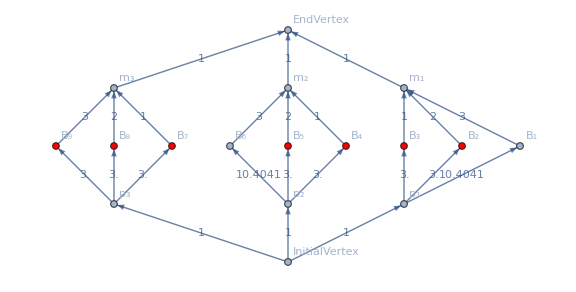
```mathematica
Export["/Users/adamjump/Desktop/SimulatedProposed.eps",-Graphics-]
```

/Users/adamjump/Desktop/SimulatedProposed.eps

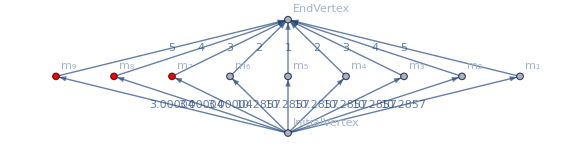
```mathematica
F=FindMinimumCostFlow[-Graphics-,"InitialVertex","EndVertex","OptimumFlowData"]
```

OptimumFlowData[<11>, <18>]

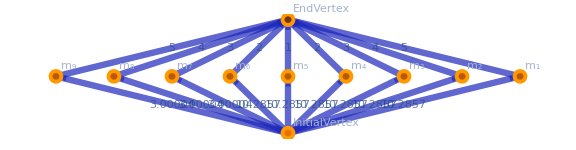

```mathematica
F["FlowGraph"]
```

```mathematica
averageSystemTime[-Graphics-]
```

4.32268

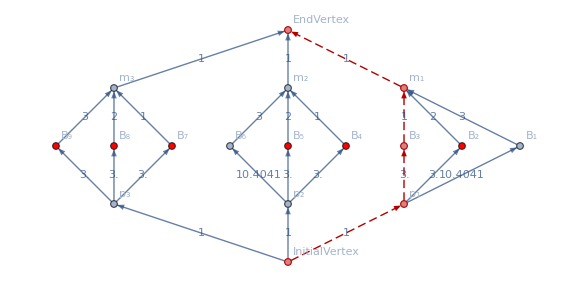

```mathematica
GraphHighlighter[-Graphics-]
```

```mathematica
currentModelGraph[9,3,6,5.6/30]
```

```mathematica
Export["/Users/adamjump/Desktop/SimulatedCurrent.eps",-Graphics-]
```

/Users/adamjump/Desktop/SimulatedCurrent.eps

```mathematica
averageSystemTime[-Graphics-]
```

11.0794

```mathematica
standardDeviationModel[-Graphics-]
```

3.3113

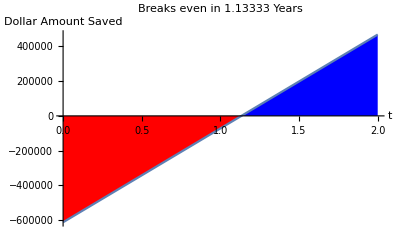

```mathematica
Clear[CostFunction]
CostFunction[t_]:=135000(LP-LC)t-65000(LP-LC)-(88000)(LP-LC)/.{LP->7,LC->3}
Plot[CostFunction[t],{t,0,2},AxesLabel->{"t","Dollar Amount Saved"},Filling->Axis,FillingStyle->{Red,Blue},PlotLabel->"Breaks even in ""1.13333"" Years"]
(*Print["Initial Cost = $",CostFunction[0]]*)
(*Print["Breaks even in ",ToString[Flatten[t/.Solve[CostFunction[t]==0,t]][[1]]//N], " Years"]*)
```